```mathematica
f[t_]:= t*Exp[-t]
g [t_]:= Exp[-t/2] - Exp[-t]
```

```mathematica
τ = 4;
```

```mathematica
int[t_]:=Expand[Integrate[g[T]*Exp[T/τ], {T, 0, t}]*Exp[-t/τ]]
```

```mathematica
int[t]
```

(4 ⅇ^-t)/3-4 ⅇ^(-t/2)+(8 ⅇ^(-t/4))/3

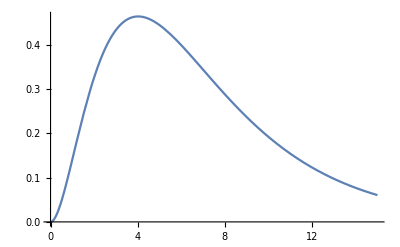

```mathematica
Plot[int[t], {t, 0, 15}]
```